```mathematica
trikotnik={{0,0},{5,1},{7,4}}
Stranice[{AA_,BB_,CC_}] := {{BB,CC},{CC,AA},{AA,BB}}
```

{{0,0},{5,1},{7,4}}

```mathematica
Koti[{AA_,BB_,CC_}] := {{CC, AA, BB},{AA, BB, CC},{BB, CC, AA}}
```

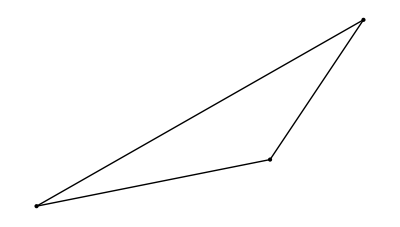

```mathematica
SlikaOglisc[trikotnik_] := Map[Point, trikotnik];
SlikaStranic[trikotnik_] :=Map[Line, Stranice[trikotnik]];
NarisiTrikotnik[trikotnik_] :=Graphics[{PointSize[Large], SlikaOglisc[trikotnik], SlikaStranic[trikotnik]},AspectRatio->Automatic]
NarisiTrikotnik[trikotnik]
```

```mathematica
VektorSimetraleKota[{x_,y_,z_}] := Normalize[Normalize[x-y]+Normalize[z-x]]
SimetralaKota[{x_,y_,z_},dol_:10] := {y,y+VektorSimetraleKotac[{x, y, z}]*dol}
```

```mathematica
(*Naloga 3*)
```

```mathematica
VektorSimetraleKota[{x_,y_,z_}] := Normalize[Normalize[x-y]+Normalize[z-x]]
SimetralaKota[{x_,y_,z_},dol_:10] := {y,y+VektorSimetraleKotac[{x, y, z}]*dol}
SlikaSimetralKotov[trikotnik_] := Map[Line,Map[SimetralaKota, Koti[trikotnik]]];
```